# Quantum States of 1-Electron Systems Using NDEigensystem

Electronic quantum eigenstates for 1 and 2 dimensional models of H and H_2^+are obtained using NDEigensystem.

## Hamiltonian operator for the Coulomb potential

Potential energy operator

```mathematica
Subscript[𝒱, 1](r__):=-1/Norm[{r}]
```

Kinetic energy operator:

```mathematica
𝒦(ψ_)(r__):=-1/2 ψ(r){r}
```

Hamiltonian operator:

```mathematica
Subscript[ℋ, 1](ψ_)(r__):=𝒦(ψ)(r)+Subscript[𝒱, 1](r) ψ(r)
```

#### Exercises:

Obtain the Hamiltonian for the Hydrogen atom in 1, 2, and 3 dimensions

Write the Schrodinger equation for the 1 dimensional Hydrogen atom.

#### Answer:

In one dimension:

```mathematica
Subscript[ℋ, 1][ψ][x]
```

-ψ[x]/Abs[x]-ψ''[x]/2

In two dimensions:

```mathematica
Subscript[ℋ, 1][ψ][x,y]
```

-ψ[x,y]/(√(Abs[x]^2+Abs[y]^2))+1/2 (-ψ^(0,2)[x,y]-ψ^(2,0)[x,y])

In 3 dimensions:

```mathematica
Subscript[ℋ, 1][ψ][x,y,z]
```

-ψ[x,y,z]/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2))+1/2 (-ψ^(0,0,2)[x,y,z]-ψ^(0,2,0)[x,y,z]-ψ^(2,0,0)[x,y,z])

## The 1-Dimension Hydrogen Atom

### Analytical solutions

Schrodinger equation for the 1 dimensional Hydrogen atom can be written as Kummer’s equation. The solutions of Kummer’s equation are the confluent hypergeometric functions Hypergeometric1F1[1-n,2, 2 x/n] .

Analytical solutions:

```mathematica
Subscript[f, n_][x_]:=x Exp[-x/n]Hypergeometric1F1[1-n,2, 2 x/n]
```

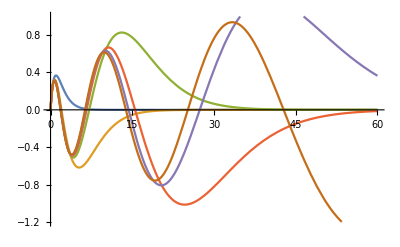

```mathematica
Plot[Evaluate@Table[Subscript[f, i][x],{i,1,6}],{x,0,60},PlotRange->{-1.2,1}]
```

In atomic units,the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 1]=Table[N[-1/(2 i^2)],{i,1,6}]
```

{-0.5,-0.125,-0.0555556,-0.03125,-0.02,-0.0138889}

#### Exercises:

Are these functions normalized? If not, find the normalization constants for each eigenstate.

Define a normalized function.

#### Answer:

Find the normalization constant for each state:

```mathematica
nint=Table[NIntegrate[(Subscript[f, n][x])^2,{x,0,100}],{n,1,6}]
```

{0.25,2.,6.75,16.,31.25,53.9357}

The normalization constant is

```mathematica
norm=1/Sqrt[nint]
```

{2.,0.707107,0.3849,0.25,0.178886,0.136164}

Normalization:

```mathematica
Subscript[Ψ, n_][x_]:=norm⟦n⟧ Subscript[f, n][x]
```

```mathematica
Table[NIntegrate[  Subscript[Ψ, i][x]^2,{x,0,100}],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

### Boundary conditions

Physically the probability of finding the electron at x=0 should be zero. Computationally, the wave function should be zero at the end of the computational box. These requirements can be fulfilled using Dirichlet Boundary conditions.

Boundary conditions:

```mathematica
Subscript[ℬ, 1]=DirichletCondition[ψ[x]==0,True];
```

In atomic units, the energies of the four lowest eigenstates are:

### Eigensystem

For a box of length l, the n lowest energy eigenstates are obtained with the function eigensystem[n,l]:

```mathematica
eigensystem1[ne_,ℓ_]:=
SortBy[
Transpose[
NDEigensystem[{Subscript[ℋ, 1][ψ][x],Subscript[ℬ, 1]},ψ,
{x,0,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],
First]
```

The eigenvalue (en) and the wave function can be obtained by using:

```mathematica
{en,wf}=eigensystem1[50,10]⟦1⟧
```

{-0.499998,InterpolatingFunction[{{0., 10.}}, <>]}

For example, for the ground state:

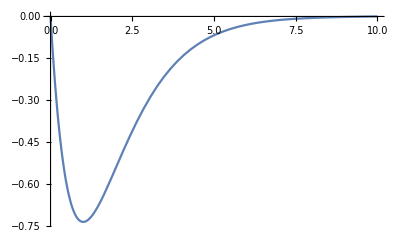

```mathematica
Plot[wf[x],{x,0,10}]
```

#### Exercise:

Verify that the eigenstates of eigensystem[n,l] are normalized.

Plot the ground state, and the first excited state. What are their energies?

#### Solution:

For example, for the 5th eigenstate obtained from a calculation of 10 states and a box of length 10 atomic units:

```mathematica
NIntegrate[(eigensystem1[10,10]⟦5,2⟧[x])^2,{x,0,10}]
```

1.

```mathematica
wf1=eigensystem1[10,10][[1,2]];
wf2=eigensystem1[10,10][[2,2]];
```

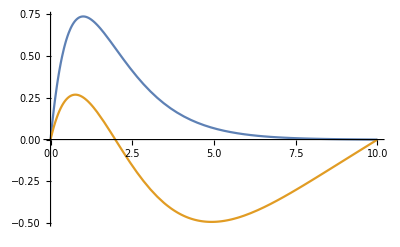

```mathematica
Plot[{wf1[x],wf2[x]},{x,0,10}]
```

### Computing the lowest energy eigenstates

Quality of the eigenvalues and eigenvectors:

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])^2,Subscript[𝒱, 1][x],Subscript[ℰ, 1]⟦i⟧+(Subscript[Ψ, i][x]^2)},{x,0,40},
PlotRange->{-0.6,0.1},
Filling->{1->es⟦i,1⟧,2-> Bottom,None}]
],
{i,1,4}
])@
eigensystem1[ne1,ℓ1],
2],
{{ℓ1,25,"Box Length"},5,40,5},
{{ne1,15,"Number of eigenfunctions"},10,40,5}
]
```

#### Investigations

Use the sliding menus of the Manipulate to explore the solutions of NDEigensystem. Answer the following questions :

Determine the range in the parameters n and l for obtaining good agreement with the analytical results

What should be the frequency of a photon to detach an electron in the 1D hydrogen atom?

What is the frequency of the emitted photon when the electron undergoes a transition between the first excited and the ground states?

## The 2-Dimension Hydrogen Atom

### Analytical solutions

#### Radial function:

The analytical radial functions are given by R[n,l,r]

```mathematica
β[n_]=2/(n-1/2);
Ν[n_,l_]:=(((n+Abs[l]-1)!)/((2 n-1)(n-Abs[l]-1)!))^(1/2);
R[n_,l_,r_]:=β[n]/((2 l)!)Ν[n,l](β[n] r)^Abs[l] Exp[-β[n] r/2]Hypergeometric1F1[-n+Abs[l]+1,2 Abs[l]+1,β[n] r];
```

Radial wave functions for l=0:

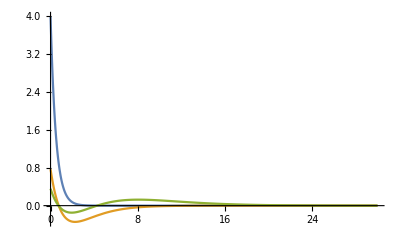

```mathematica
plotRa=Plot[Evaluate@Table[R[i,0,x],{i,1,3}],{x,0,30},PlotRange->All]
```

Radial wave functions for l=1:

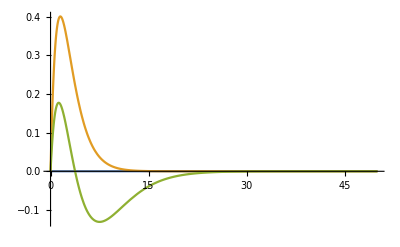

```mathematica
plotRa=Plot[Evaluate@Table[R[i,1,x],{i,1,3}],{x,0,50},PlotRange->All]
```

In atomic units, the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 2]=Table[-N[1/(2(n-1/2)^2)],{n,1,10}]
```

{-2.,-0.222222,-0.08,-0.0408163,-0.0246914,-0.0165289,-0.0118343,-0.00888889,-0.00692042,-0.00554017}

Degeneracy:

```mathematica
deg=Table[2(n-1)+1,{n,1,10}]
```

{1,3,5,7,9,11,13,15,17,19}

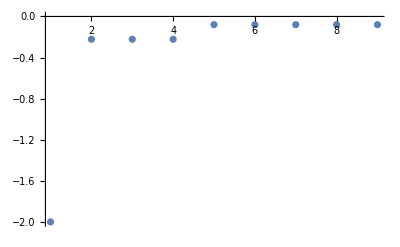

```mathematica
analyplot=ListPlot[Flatten[Table[Subscript[ℰ, 2]⟦i⟧,{i,1,3},{j,1,deg⟦i⟧}]],PlotRange->All]
```

#### Exercise

What are the differences between the eigenfunctions of the 1D and the 2D models of H aatom?

Are these functions normalized?

The wave function depends now on two quantum numbers. What is the meaning of them?

#### Answer

Numerical normalization

```mathematica
Column[Table[NIntegrate[r R[n,Abs[l],r]^2, {r,0,200}],{n,1,4},{l,-n+1,n-1}],Center ]
```

{1.}
{1.,1.,1.}
{1.,1.,1.,1.,1.}
{1.,1.,1.,1.,1.,1.,1.}

Analytically:

```mathematica
∫_0^∞ ∫_0^(2 π) r (R(2,1,r))^2 Φ(1,ϕ)Φ(-1,ϕ)ⅆϕⅆr
```

1

#### The angular function:

As we saw before, the angular part has the eigenfunctions:

```mathematica
Φ[l_,ϕ_]:=1/(√(2π))Exp[I l ϕ]
```

Plotting the angular functions Φ[l,ϕ]:

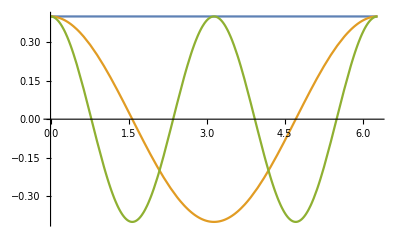

```mathematica
Plot[{Re[Φ[0,ϕ]],Re[Φ[1,ϕ]],Re[Φ[2,ϕ]]},{ϕ,0,2Pi}]
```

#### Exercise

Plot a graphics of the full wave function

Are these functions normalized?

Plot the ground state and first excited states, verify if the norm is one using polar and Cartesian coordinates.

#### Answer

The transformation from polar to Cartesian coordinates:

```mathematica
tocc=Thread[{r,ϕ}->ToPolarCoordinates[{x,y}]]
```

{r→√(x^2+y^2),ϕ→ArcTan[x,y]}

Plot the ground state:

```mathematica
Plot3D[Re[R[1,0,r]Φ[0,ϕ]]/.tocc,{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

Verify for normalization:

```mathematica
NIntegrate[Abs[R[1,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

1.

Plot the first excited state with zero angular momentum:

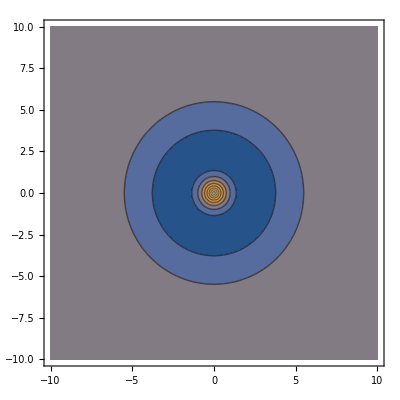

```mathematica
ContourPlot[Re[R[2,0,r]Φ[0,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->25]
```

Verify the normalization in Cartesian coordinates:

```mathematica
NIntegrate[Abs[R[2,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

0.999351

Verify for normalization in polar coordinates

```mathematica
NIntegrate[r Abs[R[2,0,r]Φ[0,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

0.998601

Plot a state with l=1:

```mathematica
Plot3D[Im[R[2,1,r]Φ[1,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

Verify normalization in polar coordinates:

```mathematica
NIntegrate[r Abs[R[2,1,r]Φ[1,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

0.999193

Verify normalization in Cartesian coordinates:

```mathematica
NIntegrate[Abs[R[2,1,r]Φ[1,ϕ]]^2/.tocc,{x,-20,20},{y,-20,20}]
```

1.

### Boundary conditions and integration region

The analytical solutions showed that there are two types of states:
- even states which are not zero at the origin
- odd states which are zero at the origin

The Dirichlet Boundary condition for the even and odd states is given by:

```mathematica
Subscript[ℬ, 2]=DirichletCondition[ψ[x,y]==0,True]
```

DirichletCondition[ψ[x,y]==0,True]

With the integration region:

```mathematica
Subscript[𝒜, 2][Rin_,Rout_]:=Annulus[{0,0},{Rin,Rout}]
```

```mathematica
Subscript[𝒟, 2][R_]:=Disk[{0,0},R];
```

The integration region looks like:

-Graphics-



```mathematica
Graphics[Subscript[𝒜, 2][0.1,1]]
Graphics[Subscript[𝒟, 2][1]]
```

#### Exercise:

Why the integration region has this form? Give a physical interpretation.

### Eigensystem with annular integration region

Define a function for the eigensystem. The number of eigenfunctions is ne, inner and outer radii of the annulus are Rin and Rout respectively:

```mathematica
eigensystem2a[ne_,Rin_,Rout_]:=
SortBy[
Transpose[NDEigensystem[{Subscript[ℋ, 1][ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒜, 2][Rin,Rout],ne,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],First]
```

Manipulate the parameters of the numerical calculation to obtain the ground state:

```mathematica
Manipulate[
(es↦
Table[
Show[
Plot3D[
es⟦i,2⟧,Evaluate[{x,y}∈Subscript[𝒜, 2][Rin,Rout]],PlotRange->All,PlotLabel->es⟦i,1⟧
]
]
,{i,1,4}
])@
eigensystem2a[ne2,Rin,Rout],
{{Rin,0.01,"Internal radius"},0.001,0.101,0.01},{{Rout,5,"External radius"},3,103,1},
{{ne2,45,"Number of eigenfunctions"},10,100,5}
]
```

#### Exercise

Find the values of the internal and external radii, and the number of eigenstates for obtaining a good approximation to the ground state.

What happened with the excited states for these parameters? How good are the numerical eigenvalues compared with the analytical ones?

Find good values of the parameters to obtain a fair agreement  with the analytical values for the energy excited states.

#### Answer

```mathematica
eigensys1=eigensystem2a[45,0.001,4];
```

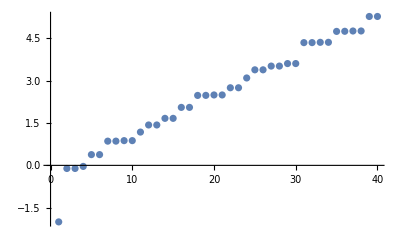

```mathematica
ListPlot[Table[{i,eigensys1⟦i,1⟧},{i,1,40}]]
```

### Eigensystem with disk integration region

Define a function for the eigensystem. The number of eigenfunctions is ne, and the radius of the disk R:

```mathematica
eigensystem2d[ne_,R_]:=
SortBy[
Transpose[NDEigensystem[{Subscript[ℋ, 1][ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒟, 2][R],ne,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],First]
```

Manipulate the parameters of the numerical calculation to obtain the ground state:

```mathematica
Manipulate[
(es↦
Table[
Show[
Plot3D[
es⟦i,2⟧,Evaluate[{x,y}∈Subscript[𝒟, 2][R]],PlotRange->All,PlotLabel->es⟦i,1⟧
]
]
,{i,1,4}
])@
eigensystem2d[ne2,R],
{{R,5,"Radius of the Disk"},3,103,1},
{{ne2,45,"Number of eigenfunctions"},10,100,5}
]
```

#### Exercise

Find the values of R, and the number of eigenstates for obtaining a good approximation to the ground state.

What happened with the excited states for these parameters? How good are the numerical eigenvalues compared with the analytical ones?

For the parameters found, plot the energy of the states. Discuss about the degeneracy.

Compare the results of using an annulus or a disk as integration region.

Find values of the parameters to obtain excited states.

#### Answer

```mathematica
eigensys2=eigensystem2d[45,5];
```

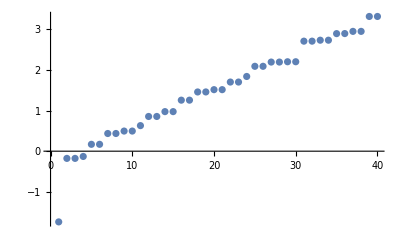

```mathematica
ListPlot[Table[{i,eigensys2⟦i,1⟧},{i,1,40}]]
```

### The potential energy surface and the ground state

Calculate the states for a Disk of radius 5:

```mathematica
esys=Table[eigensystem2d[45,5][[i]],{i,1,6}];
```

The ground state:

```mathematica
fst1=Plot3D[esys[[1,1]]+0.3Abs[esys[[1,2]]],Evaluate[{x,y}∈Disk[{0,0},2,{-Pi,Pi}]],PlotRange->All,PlotPoints->45,PlotStyle->{White,Opacity[0.8]},MeshStyle->Black]
```

-Graphics3D-

Potential energy surface:

```mathematica
fpot=Plot3D[Subscript[𝒱, 1][x,y],{x,y}∈Disk[{0,0},10,{-Pi,Pi}],PlotRange->{-2.1,0.},PlotStyle->{Opacity[0.6],Black},PlotPoints->50,MeshStyle->Gray,ColorFunction->Function[{x,y,z},RGBColor[3z, 3z,3z]],Boxed->False]
```

-Graphics3D-

The ground state in the potential energy surface:

```mathematica
Show[fpot,fst1, PlotRange->All]
```

-Graphics3D-

## The 1-Dimension Hydrogen molecule ion: H_2^+

### Hamiltonian: regularization of the Coulomb potential

Potential energy operator

```mathematica
Subscript[𝒱, 2](r__,r1__,r2__,α_):=-1/(√(Norm[{r}-{r1}]^2+α^2))-1/(√(Norm[{r}-{r2}]^2+α^2))+1/Norm[{r2}-{r1}]
```

Kinetic energy operator:

```mathematica
𝒦(ψ_)(r__):=-1/2 ψ(r){r}
```

Hamiltonian operator:

```mathematica
Subscript[ℋ, 2](ψ_)(r__,r1__,r2__,α_):=ψ(r) Subscript[𝒱, 2](r,r1,r2,α)+𝒦(ψ)(r)
```

```mathematica
Subscript[ℋ, 2][ψ][x,r1,r2,a]
```

(1/Abs[-r1+r2]-1/(√(a^2+Abs[-r1+x]^2))-1/(√(a^2+Abs[-r2+x]^2))) ψ[x]-ψ''[x]/2

A parameter α is necessary to regularize the potential energy to avoid the potential energy to blow up at singularities.

```mathematica
Manipulate[
Plot[{Subscript[𝒱, 2][x,-r/2,r/2,α],Subscript[𝒱, 2][x,-r/2,r/2,0]},{x,-6,6},PlotRange->{-6,1}],{{r,1,"Bond Length"},1,4,0.1},{{α,0.1,"Regularization Parameter"},0,2,0.2}
]
```

#### Exercises:

Find a good value for α

Plot the potential energy of H_2^+  in 1 and 2 dimensions

Obtain the Hamiltonian for the H_2^+ in 1, 2, and 3 dimensions.

Write the Schrodinger equation for the 1 dimensional H_2^+.

#### Answer:

Potential energy:

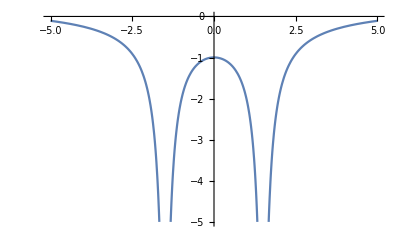

```mathematica
Plot[Subscript[𝒱, 2][x,-1.5,1.5,0.1],{x,-5,5},PlotRange->{-5,0}]
```

The potential energy in 2 dimensions:

```mathematica
Plot3D[Subscript[𝒱, 2][{x,y},{-1.5,0},{1.5,0},0.1],{x,-4,4},{y,-4,4},PlotRange->{-3,0}]
```

-Graphics3D-

### Eigensystem

The function eigensystem[l,𝓇,ne], finds ne eigenvalues of the H_2^+ for a internuclear distance 𝓇 in a computational box of length 2ℓ+𝓇 :

```mathematica
eigensystem3[ℓ_,𝓇_,ne_]:=
SortBy[
Transpose[
NDEigensystem[{Subscript[ℋ, 2][ψ][x,-𝓇/2,𝓇/2,0.1],DirichletCondition[ψ[x]==0,True]},ψ,
{x,-ℓ,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

The ground electronic state:

```mathematica
{en,wf}=eigensystem3[10.001,4,60][[1]]
```

{-3.82117,InterpolatingFunction[{{-10.001, 10.001}}, <>]}

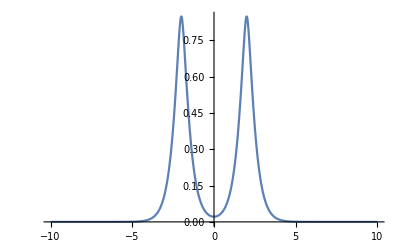

```mathematica
Plot[wf[x],{x,-10,10},PlotRange->All]
```

The first excited electronic state:

```mathematica
{en,wf}=eigensystem3[20,4,60][[2]]
```

{-3.82002,InterpolatingFunction[{{-20., 20.}}, <>]}

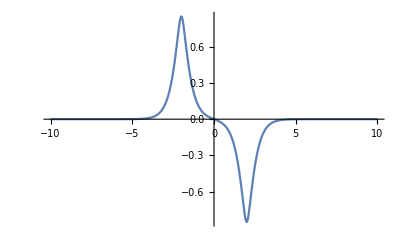

```mathematica
Plot[wf[x],{x,-10,10},PlotRange->All]
```

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x]),Subscript[𝒱, 2][x,-𝓇3/2,𝓇3/2,0.1]},{x,-ℓ3,ℓ3},
Filling->{1->es⟦i,1⟧,2-> Bottom},PlotPoints->20,PlotRange->{le,le+ΔE}]
],
{i,1,4}
])@
eigensystem3[ℓ3,𝓇3,ne3],
2],
{{ℓ3,10,"Box Length"},10,20,1},
{{𝓇3,2,"Bond Length"},1.,6.,0.5},
{{ne3,40,"Number of eigenfunctions"},40,100,5},
{{le,-2,"Lowest Energy"},-10,0,0.5},
{{ΔE,3,"Energy range"},1,20,2}
]
```

### Born Oppenheimer curves

The energy of the electronic states as a function of the internuclear distance gives the Born-Oppenheimer curves:

```mathematica
Clear[databo];databo[a_]:=databo[a]=eigensystem3[a/2+10,a,50];
```

```mathematica
tablebo=Table[Flatten[{a,Table[databo[a]⟦i,1⟧,{i,1,4}]}],{a,0.5,25.,0.2}];
```

Ground state:

```mathematica
tground=Table[
{tablebo⟦i,1⟧,tablebo⟦i,4⟧},
{i,1,Length[tablebo]}
];
```

Plot the ground state:

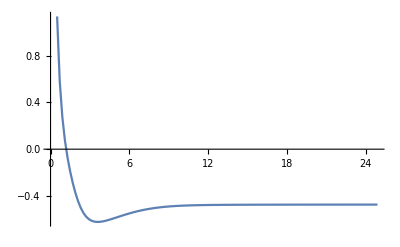

```mathematica
ground=ListLinePlot[tground,PlotRange->All]
```

First excited state

```mathematica
tfirst=Table[{tablebo⟦i,1⟧,tablebo⟦i,5⟧},{i,1,Length[tablebo]}];
```

Plot the first excited state:

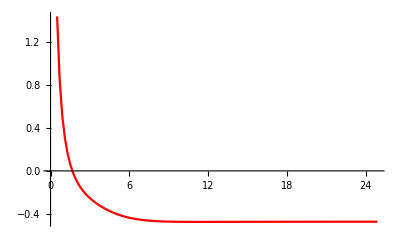

```mathematica
firste=ListLinePlot[tfirst,PlotStyle->Red,PlotRange->All]
```

The lowest electronic states (sigma)

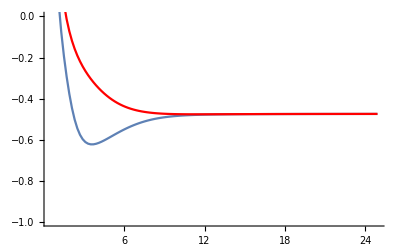

```mathematica
Show[ground,firste,PlotRange->{-1,0}]
```

#### Exercise:

Calculate the ionization energy for the hydrogen molecular ion.

Calculate the bond dissociation energy

Compare your result with the experimental value (bond length 2 atomic units and dissociation energy 2.79 eV)

Analyze the asymptotic wave functions for the ground and first excite levels

These BO curves were calculated using the 3rd and 4th eigenfunctions, not the 1st and 2nd, why?

#### Answer:

Find the lowest energy:

```mathematica
ming=Min[tground]
```

-0.622522

```mathematica
minpos=Position[tground,ming]
```

{{16,2}}

The bond lenfth at the minimum is:

```mathematica
bonding=tground[[minpos[[1,1]],1]]
```

3.5

In Angstrom is:

```mathematica
bonding*0.529
```

1.8515

The energy necessary to photo-dissociate the molecule is:

```mathematica
photo=tfirst[[minpos[[1,1]]]]-tground[[minpos[[1,1]]]]
```

{0.,0.319064}

In eV this is:

```mathematica
photo[[2]]*27.2
```

8.67854

The bonding energy in eV,  is:

```mathematica
(ming-Last[tground][[2]])*27.2
```

-4.02818

The bond length at the minimum of the ground electronic energy is:

```mathematica
tground⟦minpos⟦1,1⟧,1⟧
```

3.5

```mathematica
states1to4=Table[eigensystem3[20,1.3,50][[i]],{i,1,4}];
```

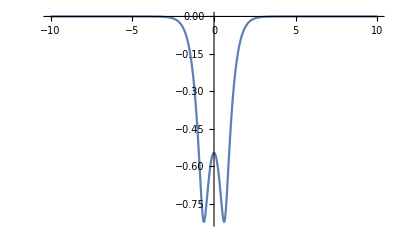
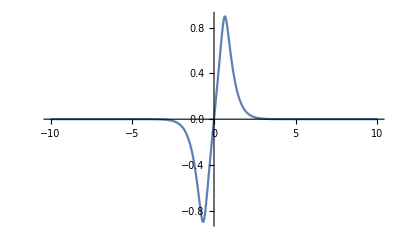
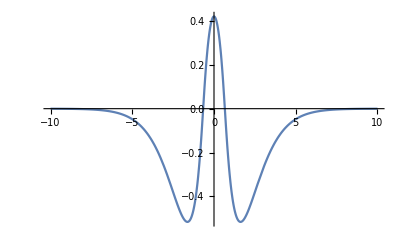
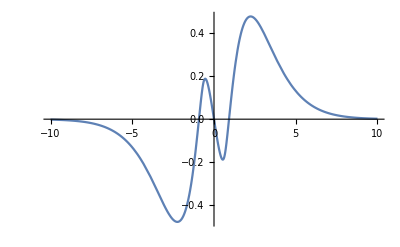

```mathematica
Table[Plot[states1to4[[i,2]][x],{x,-10,10},PlotRange->All],{i,1,4}]
```

## The 2-Dimension Hydrogen molecule ion: H_2^+

### Redefining the Hamiltonian: List and Sequence

```mathematica
Subscript[𝒱, 22](r_,r1_,r2_,α_):=-1/(√(Norm[{r}-{r1}]^2+α^2))-1/(√(Norm[{r}-{r2}]^2+α^2))+1/Norm[{r2}-{r1}]
```

Kinetic energy operator:

```mathematica
Subscript[𝒦, 2][ψ_][r_]:=-1/2 ψ[r/.List->Sequence]{r/.List->Sequence}
```

Hamiltonian operator:

```mathematica
Subscript[ℋ, 22][ψ_][r_,r1_,r2_,α_]:=ψ[r/.List->Sequence] Subscript[𝒱, 22][r,r1,r2,α]+Subscript[𝒦, 2][ψ][r]
```

### Eigensystem and lowest energy states

```mathematica
eigensystem4[ℓ_,𝓇_,ne_]:=
SortBy[
Transpose[
NDEigensystem[{Subscript[ℋ, 22][ψ][{x,y},{-𝓇/2,0},{𝓇/2,0},0.1],DirichletCondition[ψ[x,y]==0,True]},ψ,
{x,-ℓ,ℓ},{y,-ℓ,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}}}]],
First]
```

Find the ground state

```mathematica
esys=eigensystem4[7.001,4,50];
```

```mathematica
{en,wf}=esys[[1]]
```

{-1.31018,InterpolatingFunction[{{-7.001, 7.001}, {-7.001, 7.001}}, <>]}

Plot the ground state:

```mathematica
Plot3D[wf[x,y],{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->25]
```

-Graphics3D-

Find the excited state:

```mathematica
{en,wf}=esys[[2]]
```

{-1.28132,InterpolatingFunction[{{-7.001, 7.001}, {-7.001, 7.001}}, <>]}

Plotting the first excited state:

```mathematica
Plot3D[wf[x,y],{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->25]
```

-Graphics3D-

```mathematica
Manipulate[
(es↦Table[
Plot3D[es⟦i,2⟧[x,y],{x,-ℓ4,ℓ4},{y,-ℓ4,ℓ4},
PlotPoints->20,PlotRange->All],
{i,1,2}])@
eigensystem4[ℓ4,𝓇4,ne4],
{{ℓ4,7.001,"Box Length"},6.001,14.001,2},
{{𝓇4,4.0,"Bond Length"},2.,6.,0.5},
{{ne4,50,"Number of eigenfunctions"},40,60,5}
]
```

Further Explorations

Beyond the Born Oppenheimer approximation

Born Oppenheimer Curves for 2 Dimensional Hydrogen molecule ion.

Electronic correlation for the 1-dimension H_2 molecule or He atom.

Matching boundary conditions at boundaries of integration regions

Authorship information

Carlos A. Arango

05/07/2017

caarango@icesi.edu.co